```mathematica
ClearAll["Global`*"]
```

```mathematica
namelist={"putin","obama","francis","merkel","gates","bernanke","Abdullah","draghi","Michael%20Dule","Helu","Buffett","Kequiang"};

Do[
name[n]=namelist[[n]];

F =Import["/Users/danielgladstone/Documents/twitter_project/graph/"<>name[n]];

GList[n]=Table[
joined=First[F[[i]]]->Last[F[[i]]]
,{i,1,Length[F]}];
G=Graph[GList[n]];
VC[n]=VertexCount[G];
VID[n]=Mean[VertexInDegree[G]];
CC[n]=Mean[ClosenessCentrality[G]];
GD[n]=GraphDensity[G];
GR[n]=GraphReciprocity[G];
GCC[n]=GlobalClusteringCoefficient[G];
GA[n]=GraphAssortativity[G];
MND[n]=Mean[MeanNeighborDegree[G]];
MDC[n]=Mean[MeanDegreeConnectivity[G]];

,{n,Length[namelist]}]
```

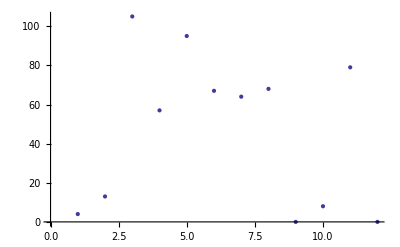

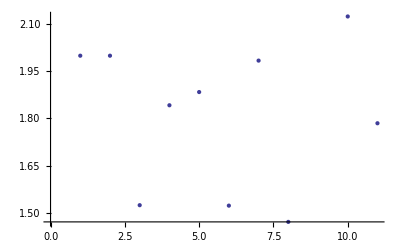

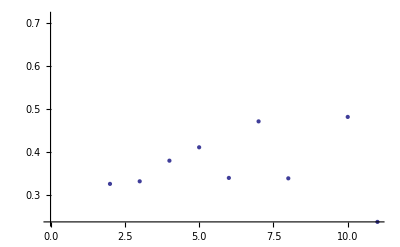

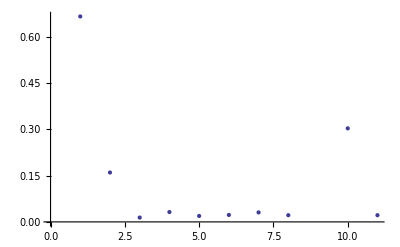

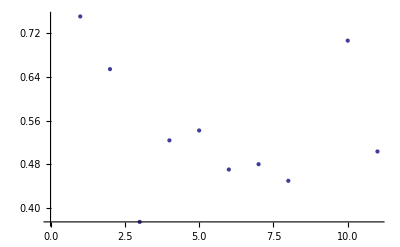

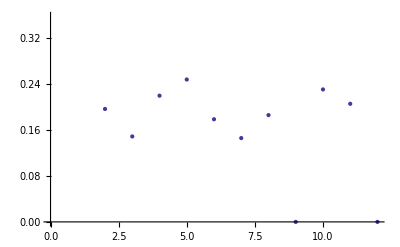

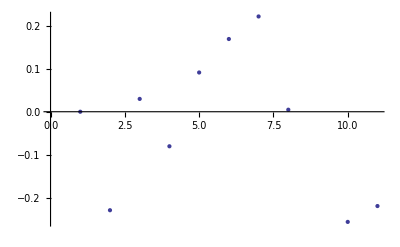

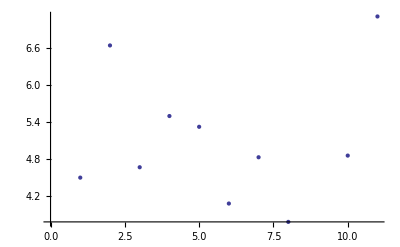

```mathematica
ListPlot[Table[VC[j],{j,Length[namelist]}]]
ListPlot[Table[VID[j],{j,Length[namelist]}]]
ListPlot[Table[CC[j],{j,Length[namelist]}]]
ListPlot[Table[GD[j],{j,Length[namelist]}]]
ListPlot[Table[GR[j],{j,Length[namelist]}]]
ListPlot[Table[GCC[j],{j,Length[namelist]}]]
ListPlot[Table[GA[j],{j,Length[namelist]}]]
ListPlot[Table[MND[j],{j,Length[namelist]}]]
ListPlot[Table[MDC[j],{j,Length[namelist]}]]
```

```mathematica
Range[Length[namelist]]
Table[VC[j],{j,Length[namelist]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

{4,13,105,57,95,67,64,68,0,8,79,0}

```mathematica
G=Graph[GList]

VertexCount[G]
Mean[VertexInDegree[G]]
Mean[ClosenessCentrality[G]]
GraphDensity[G]
GraphReciprocity[G]
GlobalClusteringCoefficient[G]
GraphAssortativity[G]
Mean[MeanNeighborDegree[G]]
Mean[MeanDegreeConnectivity[G]]
```

-Graphics-

4

2

0.9375

2/3

3/4

3/5

0

9/2

7/3

```mathematica
First[F[[1]]]->Last[F[[1]]]
```

#cat→#cats

```mathematica
.
```

```mathematica
Table[
Print[i];
,{i,2,5}]
```

2

3

4

5

{Null,Null,Null,Null}